```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
Get["../../lib/lib2.m"];
Get["../../lib/util.m"];
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools,newtxtext,newtxmath}"}, FontSize->12];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
texStyle={FontFamily->"Times",FontSize->12};
```

```mathematica
cm = 72/2.54;
```

```mathematica
plotsDir = "../../../plots/plots-thesis";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
data = Import["../../../runs/Trials/N9K9/21385198.dat"];
```

```mathematica
changeNK[9, 9];
```

```mathematica
c = Covariance[data[[All, 2;;$K(($N)^2-1)+1]]];
```

```mathematica
fig = Histogram[{Table[c[[i, i]]/c[[1, 1]], {i, 1, $K(($N)^2-1)}], Flatten@Table[c[[i, j]]/c[[1, 1]], {i, 1, $K(($N)^2-1)}, {j,i+1,$K($N^2-1)}]}, 350, PDF, 
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
FrameLabel->MaTeX/@{"\\frac{c_{i a, j b}}{c_{1 1, 1 1}}", "\\text{relative frequency}"},
FrameTicks->{{With[{ticks=0+3Range[0,6]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=0.0 + 0.2Range[0,8]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
ChartLegends->Placed[MaTeX/@{"\\text{diagonal}", "\\text{off-diagonal}"}, {Bottom, Bottom}],
ImageSize->14cm,
GridLines->{{0, 1}, None},
PlotRange->All
];
```

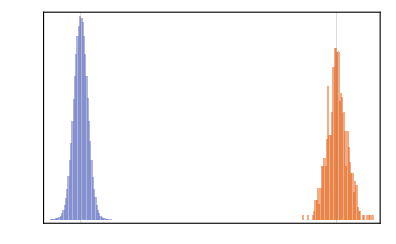

```mathematica
Magnify[fig, 1]
```

```mathematica
Export[plotsDir<>"/8-elements-covariance.pdf", fig]
```

../../../plots/plots-thesis/8-elements-covariance.pdf